## Sideband cooling

```mathematica
ΩR=0.1;
η=0.15;
M[n_]:=(ΩR/2 η)^2 n;
γ[n_]:=η^2 n ;

Rule2Matrix[tab_]:=Normal@SparseArray[Flatten@tab,{14,14}];
(*Araman=Rule2Matrix@Table[{{n+1,n+7}->M[n],{n+7,n+7}->-M[n],{n+1,n+1}->-M[n],{n+7,n+1}->M[n]},{n,1,6}];*)
Araman=(ΩR/2)^2 Rule2Matrix@Table[{{n+1,n+8}->1,{n+8,n+8}->-1,{n+1,n+1}->-1,{n+8,n+1}->1},{n,0,6}];
Apump=Rule2Matrix@Table[{{n+1,n+8}->1,{n+8,n+8}->-1},{n,0,6}]+Rule2Matrix@Table[{{n+1,n+7}->γ[n],{n+7,n+7}->-γ[n]},{n,1,6}]+Rule2Matrix@Table[{{n+1,n+9}->γ[n+1],{n+9,n+9}->-γ[n+1]},{n,0,5}];
```

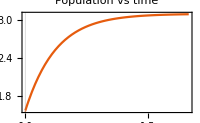

```mathematica
pi=Table[Exp[-0.4 n],{n,0,6}]~Join~ConstantArray[0,7];
pi/=Total[pi];
population[t_]:=(MatrixExp[(Araman+Apump)t].pi)[[1;;7]];
fig1=ListPlot[{population[0],population[50000],population[200000]},DataRange->{0,6},PlotRange->{0,.5},PlotTheme->"Scientific",
PlotLegends->Placed[{"","",""},Right],
Filling->Axis,PlotMarkers->"OpenMarkers",
FrameLabel->{""," "},PlotLabel->"Population distribution",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200];

avgn[t_]:=(MatrixExp[(Araman+Apump)t].pi)[[1;;7]].{0,1,2,3,4,5,6};
fig2=Plot[avgn[t*10^5],{t,0,2},PlotRange->Full,PlotTheme->"Scientific",
FrameLabel->{""," "},PlotLabel->"Population vs time",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200];

GraphicsRow[{fig1,fig2}]
```

```mathematica
Export["/Users/hongyi/Desktop/dn=0.pdf",%545,"PDF"]
```

/Users/hongyi/Desktop/dn=0.pdf

```mathematica
Δ=5.;
M[n_]:=(ΩR/2 η)^2 n;
Mdetune[n_]:=M[n]/(1+Δ^2/M[n]);
Araman=Rule2Matrix@Table[{{n+1,n+7}->Mdetune[n],{n+7,n+7}->-Mdetune[n],{n+1,n+1}->-Mdetune[n],{n+7,n+1}->Mdetune[n]},{n,1,6}];
Araman+=(ΩR/2)^2/(1+(2Δ/ΩR)^2)Rule2Matrix@Table[{{n+1,n+8}->1,{n+8,n+8}->-1,{n+1,n+1}->-1,{n+8,n+1}->1},{n,0,6}];
```

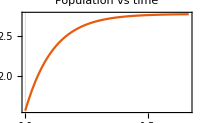

```mathematica
pi=Table[Exp[-0.4 n],{n,0,6}]~Join~ConstantArray[0,7];
pi/=Total[pi];
population[t_]:=(MatrixExp[(Araman+Apump)t].pi)[[1;;7]];
fig1=ListPlot[{population[0],population[5*^8],population[2*^9]},DataRange->{0,6},PlotRange->{0,.5},PlotTheme->"Scientific",
PlotLegends->Placed[{"","",""},Right],
Filling->Axis,PlotMarkers->"OpenMarkers",
FrameLabel->{""," "},PlotLabel->"Population distribution",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200];

avgn[t_]:=(MatrixExp[(Araman+Apump)t].pi)[[1;;7]].{0,1,2,3,4,5,6};
fig2=Plot[avgn[t*10^9],{t,0,2},PlotRange->Full,PlotTheme->"Scientific",
FrameLabel->{""," "},PlotLabel->"Population vs time",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200];

GraphicsRow[{fig1,fig2}]
```

```mathematica
Export["/Users/hongyi/Desktop/dn=-0.5.pdf",%594,"PDF"]
```

/Users/hongyi/Desktop/dn=-0.5.pdf

## Feshbach resonance

```mathematica
ClearAll["`*"]
```

```mathematica
V={{qo^2,Ω},{Ω,qc^2}};
Eigensystem@V
```

{{1/2 (qc^2+qo^2-√(qc^4-2 qc^2 qo^2+qo^4+4 Ω^2)),1/2 (qc^2+qo^2+√(qc^4-2 qc^2 qo^2+qo^4+4 Ω^2))},{{-(qc^2-qo^2+√(qc^4-2 qc^2 qo^2+qo^4+4 Ω^2))/(2 Ω),1},{-(qc^2-qo^2-√(qc^4-2 qc^2 qo^2+qo^4+4 Ω^2))/(2 Ω),1}}}

```mathematica
f[r_]:=(Cos[θ]Sin[q1 r])/r-(A Sin[θ]Sin[q2 r])/r;
f[r]/f'[r]/.{A->-Tan[θ] Sin[q1 r]/Sin[q2 r]}//FullSimplify
```

r/(Cos[θ]^2 (-1+q1 r Cot[q1 r])+(-1+q2 r Cot[q2 r]) Sin[θ]^2)

## Bose-Hubbard

```mathematica
ClearAll["`*"]
```

a band structure

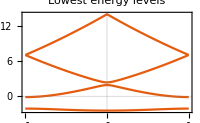

```mathematica
HBZ[q_,Vlat_]:=SparseArray[Table[{l+11,l+11}->(2l+q)^2+Vlat/2,{l,-10,10}]~Join~{Band[{1,2}]->-Vlat/4,Band[{2,1}]->-Vlat/4},{21,21}];
Vlat=4.;
Plot[Eigenvalues[HBZ[q,Vlat],-4]-Vlat,{q,-1,1},PlotTheme->"Scientific",FrameLabel->{""," "},PlotLabel->"Lowest energy levels",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
```

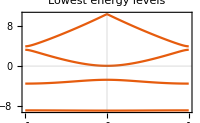

```mathematica
Vlat=12.;
Plot[Eigenvalues[HBZ[q,Vlat],-4]-Vlat,{q,-1,1},PlotTheme->"Scientific",FrameLabel->{""," "},PlotLabel->"Lowest energy levels",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
```

b lowest band wave function

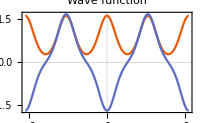

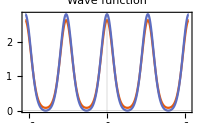

```mathematica
wf[q_]:=With[{u=Flatten@Eigenvectors[HBZ[q,8.],-1]},
ϕ=Exp[ⅈ q x]ListCorrelate[u,Table[Exp[2ⅈ l x],{l,-10,10}]]];
Plot[{Re@wf[0],Re@wf[1]},{x,-2π,2π},PlotTheme->"Scientific",FrameLabel->{""," "},PlotLabel->"Wave function",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
Plot[{Abs[wf@0]^2,Abs[wf@1]^2},{x,-2π,2π},PlotTheme->"Scientific",FrameLabel->{""," "},PlotLabel->"Wave function",
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
```

c Tunneling=lowest band width/4

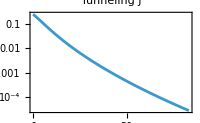

```mathematica
J[Vlat_]:=Abs[Eigenvalues[HBZ[1.,Vlat],-1]-Eigenvalues[HBZ[0.,Vlat],-1]]/4;

LogPlot[J[Vlat],{Vlat,0,50},PlotTheme->"Detailed",
FrameLabel->{""," "},PlotLabel->"Tunneling J",PlotLegends->None,
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
```

d Lowest band Wannier functions at

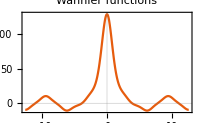

```mathematica
Vlat=3.;
c[n_,q_]:=Flatten@Eigenvectors[HBZ[q,Vlat],{-n}];
ϕ[n_,q_,x_]:=Exp[ⅈ q x]First@ListCorrelate[c[n,q],Table[Exp[2ⅈ l x],{l,-10,10}]];
dq=0.02;
w[n_,x_]:=Sum[ϕ[n,q,x],{q,-1+dq,1,dq}];
Plot[-Re@w[1,x],{x,-4π,4π},PlotRange->Full,PlotTheme->"Scientific",
FrameLabel->{""," "},PlotLabel->"Wannier functions",PlotLegends->None,
FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->10],
ImageSize->200]
```